# RFA for Square-Well, Square-Shoulder, and Nonadditive Hard-Sphere Mixtures

Annotated implementation accompanying the paper. This notebook is intended as a transparent research implementation rather than a software package.

## How to use this notebook

1. Evaluate the initialization cells from the beginning in a fresh Mathematica kernel.
2. Modify only the parameters in the clearly marked case-study section.
3. Run the coefficient-determination section before evaluating correlation functions.

The implementation follows the notation of the paper and is formulated for multicomponent mixtures with arbitrary compositions and core diameters. However, a common shell width, Δ_ij=Δ, is assumed.

## Numerical note

The inverse Laplace transform is evaluated numerically. The numerical accuracy should be checked if the notebook is used for parameter ranges substantially different from those considered here.

## Initialization

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

## Numerical Laplace inversion routine

```mathematica
Details in https://github.com/SantosBravo/Numerical-Inverse-Laplace-Transform-Abate-Whitthttps://github.com/SantosBravo/Numerical-Inverse-Laplace-Transform-Abate-WhittNonehttps://github.com/SantosBravo/Numerical-Inverse-Laplace-Transform-Abate-WhittHyperlinkActionRecycledHyperlinkActive
```

```mathematica
EulerILT[funs_,t_,argu_List]:=Module[{
aa=19.1,ntr=15,mEuler=11, 
hh=N[Pi/t],suma,avgsu=0.,c,xx,su,uu,nn},
c[m_]:=c[m]=Binomial[mEuler,m-1];
uu=Exp[aa/2.]/t;
xx=aa/(2.*t);
su[1]=Re[ funs[xx,argu] ]/2.+Sum[(-1)^nn*Re[funs[xx+I*nn*hh,argu]],{nn,1,ntr}];
Do[nn=ntr+k;
su[k+1]= su[k]+(-1)^nn*Re[funs[xx+I*nn*hh,argu]],{k,1,mEuler+1}];
Do[avgsu= avgsu+c[j]*su[j] ,{j,1,mEuler+1}];
 uu*avgsu/2^mEuler 
]
```

EulerILTplus is a slower but more accurate version of EulerILT

```mathematica
EulerILTplus[funs_,t_,argu_List,preci_:$MachinePrecision]:=Module[{
aa=30,ntr=100,mEuler=30, (* new values for  A=aa, n=ntr and m=mEuler *)
hh=N[Pi/t,preci],avgsu=0,c,xx,su,uu,nn},
c[m_]:=c[m]=Binomial[mEuler,m-1];
uu=N[Exp[aa/2]/t,preci];
xx=N[aa/(2*t),preci];
su[1]=Re[N[funs[xx,argu]/2,preci]]+Sum[(-1)^nn*Re[N[funs[xx+I*nn*hh,argu],preci]],{nn,1,ntr}];
Do[nn=ntr+k;
su[k+1]=N[su[k]+(-1)^nn*Re[N[funs[xx+I*nn*hh,argu],preci]],preci],{k,1,mEuler+1}];
Do[avgsu=N[avgsu+c[j]*su[j],preci],{j,1,mEuler+1}];
N[uu*avgsu/2^mEuler,preci]
]
```

## Case to be studied

#### Example of a ternary SW mixture

```mathematica
nco=3 (* number of components *);
xcon={0.7,0.2,0.1} (* mole fractions *);
sigmas={1,1.5,2} (* diameters *);
eps={{-1,-0.9,-0.8},{-0.9,-0.7, -0.6},{-0.8, -0.6, -0.5}} (* energy barriers *);
Delta=0.1 (* common width *);
rho=0.2 (* density *);
β=1 (* inverse temperature *);
```

```mathematica
tol=10^-10;
If[!SymmetricMatrixQ[eps],Print["Warning: eps is not symmetric!"]]
If[Abs[Total[xcon]-1]>tol,Print["Warning: the sum of the mole fractions is not equal to 1!"]]
```

## Determination of the RFA coefficients

```mathematica
Do[x[n]=xcon[[n]];
sig[n,n]=sigmas[[n]],{n,1,nco}];
sig[i_,j_]:=1/2*(sig[i,i]+sig[j,j])/;i!=j;
λ[i_,j_]:=sig[i,j]+Delta;
ϵ[i_,j_]:=eps[[i,j]]
```

```mathematica
sigmaMin=Min[sigmas];
```

```mathematica
(* Eq. (59): Subscript[Λ, j] *)
Λ[j_]:=(1+Pi*rho*Sum[x[k]*(L1[k,j]*sig[k,k]^2+Lb1[k,j]*λ[k,k]^2),{k,1,nco}])/(1+Pi/3*rho*Sum[x[k]* (Exp[-β*ϵ[k,j]]*sig[k,k]^3-(Exp[-β*ϵ[k,j]]-1) λ[k,k]^3),{k,1,nco}])
```

```mathematica
(* Eq. (58): Subscript[L, ij]^(0) *)
L0[i_,j_]:=Λ[j]*Exp[- β*ϵ[i,j]]
```

```mathematica
(* Eq. (58): Subscript[L̄, ij]^(0) *)
Lb0[i_,j_]:=Λ[j]*(1-Exp[-β*ϵ[i,j]])
```

```mathematica
(* Eq. (55): impose the low-s consistency condition to obtain Subscript[L, ij]^(1) in terms of Subscript[L̄, ij]^(1) *)
sysEq=Table[L1[i,j]==-Lb1[i,j]+Lb0[i,j]*Delta+sig[i,j]+
Pi*rho*Sum[x[k]*sig[i,k](L1[k,j]*sig[k,k]^2+ Lb1[k,j]*λ[k,k]^2  - L0[k,j]*sig[k,k]^3/3-Lb0[k,j]*λ[k,k]^3/3   ),{k,1,nco}]+
Pi/3*rho*Sum[x[k](L0[k,j]*sig[k,k]^4/4+Lb0[k,j]*λ[k,k]^4/4-L1[k,j]*sig[k,k]^3- Lb1[k,j]*λ[k,k]^3  ),{k,1,nco}],{i,1,nco},{j,1,nco}]//Flatten//Simplify;
```

```mathematica
var=Table[L1[i,j],{i,1,nco},{j,1,nco}]//Flatten;
```

```mathematica
sol=Solve[sysEq,var]//Flatten;
```

```mathematica
(* Solution of Eq. (55): Subscript[L, ij]^(1) in terms of Subscript[L̄, ij]^(1) *)
Table[L1[i,j]=L1[i,j]/.sol//Flatten,{i,1,nco},{j,1,nco}];
```

```mathematica
(* Eq. (30): Subscript[L, ij](s) *)
LMatrix=Table[L0[i,j]+L1[i,j]*s,{i,1,nco},{j,1,nco}];
```

```mathematica
(* Eq. (30): Subscript[L̄, ij](s) *)
LbMatrix=Table[Lb0[i,j]+Lb1[i,j]*s,{i,1,nco},{j,1,nco}];
```

```mathematica
(* Eq. (45): Subscript[Â, ij](s) *)
Ahat[i_,j_,s_]:=2*Pi*rho*x[i]*(-Lb0[i,j]-L0[i,j]+
(L0[i,j]*sig[i,i]+Lb0[i,j]*λ[i,i]-L1[i,j]-Lb1[i,j])*s+
(-Lb0[i,j]*λ[i,i]^2/2-L0[i,j]*sig[i,i]^2/2+L1[i,j]*sig[i,i]+Lb1[i,j]*λ[i,i])*s^2)
```

```mathematica
AhatMatrix=Table[Ahat[i,j,s],{i,1,nco},{j,1,nco}];
```

```mathematica
(* Eq. (44): Subscript[Ξ, ij](s)*)
XiMatrix=s(LMatrix.Inverse[s^3*IdentityMatrix[nco]+AhatMatrix]) ;
```

```mathematica
(* Eq. (47): Subscript[Ξ̄, ij](s)*)
XibMatrix=s(LbMatrix.Inverse[s^3*IdentityMatrix[nco]+AhatMatrix]) ;
```

```mathematica
(* Inverse Laplace transform of  Subscript[Ξ, ij](s): Subscript[ξ, ij](r) *)
xi[r_?NumericQ,i_,j_,Lb1V_?(MatrixQ[#,NumericQ]&)]:=InverseLaplaceTransform[XiMatrix[[i,j]]/. Flatten[Table[Lb1[k,l]->Lb1V[[k,l]],{k,1,nco},{l,1,nco}]],s,r]
```

```mathematica
(* Subscript[ξ, ij](Δ) *)
xiDelta[i_,j_,Lb1V_?(MatrixQ[#,NumericQ]&)]:=xi[Delta,i,j,Lb1V];
```

```mathematica
(* Eq. (56): impose the continuity of the cavity functions to obtain Subscript[L̄, ij]^(1) *)solu=FindRoot[Flatten[Table[Lb1[i,j]==(Exp[β*ϵ[i,j]]-1)*xiDelta[i,j,Table[Lb1[k,l],{k,1,nco},{l,1,nco}]],{i,1,nco},{j,1,nco}]],InitialValues,Method->{"Newton","StepControl"->Automatic}]//Chop;
```

```mathematica
Table[ILT[i,j]=InverseLaplaceTransform[XiMatrix[[i,j]]/.solu,s,rr],{i,1,nco},{j,1,nco}];
```

```mathematica
Table[ILTb[i,j]=InverseLaplaceTransform[XibMatrix[[i,j]]/.solu,s,rr],{i,1,nco},{j,1,nco}];
```

```mathematica
(* Inverse Laplace transform of  Subscript[Ξ, ij](s): Subscript[ξ, ij](r) *)
xiFINAL[r_?NumericQ,i_,j_]:=If[r==0,L1[i,j]/.solu,ILT[i,j]/.rr->r]//Re
```

```mathematica
(* Inverse Laplace transform of  Subscript[Ξ̄, ij](s): Subscript[ξ̄, ij](r) *)
xibFINAL[r_?NumericQ,i_,j_]:=If[r==0,Lb1[i,j]/.solu,ILTb[i,j]/.rr->r]//Re
```

## g_ij(r), y_ij(r) & (h̃)_ij(q)

```mathematica
(* Eq. (21): Subscript[φ, m](x) *)
φ1[x_]:=Exp[-x]-1+x;
φ2[x_]:=Exp[-x]-1+x-x^2/2;
```

```mathematica
(* Eq. (39b): Subscript[A, ij](s) *)
A[i_,j_,s_]:=2*Pi*rho*x[i]/s^3*(  L0[i,j]*φ2[sig[i,i]*s]+ L1[i,j]*s*φ1[sig[i,i]*s]+Lb0[i,j]*φ2[λ[i,i]*s]+Lb1[i,j]*s*φ1[λ[i,i]*s])
```

```mathematica
AMatrix=Table[A[i,j,s],{i,1,nco},{j,1,nco}];
```

```mathematica
(* Eq. (39a): First term in Subscript[G, ij]^0(s)s^2 ⅇ^(s Subscript[σ, ij]) *)
GG0Matrix=LMatrix.Inverse[IdentityMatrix[nco]+AMatrix]/.solu//Simplify;
```

```mathematica
(* Eq. (39a): Second term in Subscript[G, ij]^0(s)s^2 ⅇ^(s Subscript[σ, ij]) *)
GG0bMatrix=LbMatrix.Inverse[IdentityMatrix[nco]+AMatrix]/.solu//Simplify;
```

```mathematica
(* Eq. (6): Subscript[h̃, ij]^0(q) *)
htilde0Asyimm[q_,i_,j_]:=-4π Re [1/s^3(Exp[-sig[i,j]s]GG0Matrix[[i,j]]+Exp[-λ[i,j]s]GG0bMatrix[[i,j]]-1)/.s->I q]
```

```mathematica
(* Symmetrization of Subscript[h̃, ij]^0(q) *)
htilde0[q_,i_,j_]:=If[i==j,htilde0Asyimm[q,i,j],(htilde0Asyimm[q,i,j]+htilde0Asyimm[q,j,i])/2]
```

```mathematica
ClearAll[myfun1,myfun2]
```

```mathematica
myfun1[ss_?NumericQ,{i_,j_}]:=myfun1[ss,{i,j}]=GG0Matrix[[i,j]]/s^2/. s->ss
```

```mathematica
myfun2[ss_?NumericQ,{i_,j_}]:=myfun2[ss,{i,j}]=GG0bMatrix[[i,j]]/s^2/. s->ss
```

```mathematica
(*Inverse Laplace transform of Subscript[G, ij]^0(s): Subscript[g, ij]^0(r) by means of the EulerILT algorithm *)
g0Asymm[r_,i_,j_]:=Which[r<sig[i,j],0,r<=λ[i,j],xiFINAL[r-sig[i,j],i,j]/r,r<=sig[i,j]+sigmaMin,xiFINAL[r-sig[i,j],i,j]/r+xibFINAL[r-λ[i,j],i,j]/r,r>sig[i,j]+sigmaMin,
EulerILT[myfun1, r-sig[i,j],{i,j}]/r+EulerILT[myfun2, r-λ[i,j],{i,j}]/r]
```

```mathematica
(* Symmetrization of Subscript[g, ij]^0(r) *)
g0[r_,i_,j_]:=If[i==j,g0Asymm[r,i,j],(g0Asymm[r,i,j]+g0Asymm[r,j,i])/2]
```

```mathematica
(* Eq. (7): Subscript[y, ij]^0(r) *)
y0[r_,i_,j_]:=If[r<=λ[i,j],
Exp[β*ϵ[i,j]]*g0[r,i,j],g0[r,i,j]]
```

```mathematica
(* Eq. (53b): Subscript[ξ̄, ij]'(0) *)
xibPrimeZero[i_,j_]:=Lb0[i,j]-2*Pi*rho*Sum[Lb1[i,k]*x[k]*(
L1[k,j]*sig[k,k]+Lb1[k,j]*λ[k,k]-L0[k,j]*sig[k,k]^2/2-Lb0[k,j]*λ[k,k]^2/2),{k,1,nco}]/.solu
```

```mathematica
(* Laplace transform of Subscript[ξ, ij]'(r) *)
XiPrimeMatrix[i_,j_]:=s*XiMatrix[[i,j]]-L1[i,j]/.solu//Simplify//Chop
```

```mathematica
(* Subscript[ξ, ij]'(r) *)
xiPrime[r_,i_,j_]:=InverseLaplaceTransform[XiPrimeMatrix[i,j],s,rr]/.rr->r//Re
```

```mathematica
(*Eq. (51): Subscript[μ, ij] *)
mu[i_,j_]:=1/λ[i,j](xibPrimeZero[i,j]+(1-Exp[β*ϵ[i,j]])*xiPrime[Delta,i,j])
```

```mathematica
(* Eq. (34): Subscript[Q, ij](r) *)
Q[r_?NumericQ,i_,j_]:=mu[i,j]r(r-λ[i,j])/λ[i,j]
```

```mathematica
(* Fourier transform of Subscript[Q, ij](r) *)
Qtilde[q_,i_,j_]:=(4π mu[i,j])/(q^5 λ[i,j])(4 q λ[i,j] Cos[q λ[i,j]]+q (2 λ[i,j]-6 sig[i,j]-q^2 λ[i,j] sig[i,j]^2+q^2 sig[i,j]^3) Cos[q sig[i,j]]+(-6+q^2 λ[i,j]^2) Sin[q λ[i,j]]+(6+q^2 (2 λ[i,j]-3 sig[i,j]) sig[i,j]) Sin[q sig[i,j]])
```

```mathematica
(* Subscript[h̃, ij](q) *)
htilde[q_,i_,j_]:=htilde0[q,i,j]+Exp[-β*ϵ[i,j]]*Qtilde[q,i,j]
```

```mathematica
(* Subscript[g, ij](r) *)
g[r_,i_,j_]:=g0[r,i,j]+If[sig[i,j]<=r<=λ[i,j],
Exp[-β*ϵ[i,j]]Q[r,i,j],0]
```

```mathematica
(* Subscript[y, ij](r) *)
y[r_,i_,j_]:=y0[r,i,j]+If[sig[i,j]<=r<=λ[i,j],
Q[r,i,j],0]
```

## Some numerical results for the case of study

Evaluation of y_11(r) from r=σ_11 up to r=rmax in steps of size Deltar

```mathematica
With[{i=1,j=1,rmax=5,Deltar=0.1},yExample[i,j]=Table[{r,y[r,i,j]},{r,sig[i,j],rmax,Deltar}]]
```

{{1.,1.31774},{1.1,1.23826},{1.2,1.1672},{1.3,1.10897},{1.4,1.0628},{1.5,1.02799},{1.6,1.00391},{1.7,0.99001},{1.8,0.985811},{1.9,0.990889},{2.,1.00489},{2.1,1.00034},{2.2,0.986373},{2.3,0.986227},{2.4,0.989154},{2.5,0.996043},{2.6,0.996454},{2.7,0.994213},{2.8,0.996584},{2.9,0.998877},{3.,1.00369},{3.1,1.004},{3.2,1.00193},{3.3,1.00162},{3.4,1.00072},{3.5,1.00071},{3.6,1.00079},{3.7,0.999881},{3.8,0.999556},{3.9,0.999984},{4.,1.00012},{4.1,0.999854},{4.2,0.999689},{4.3,0.999791},{4.4,0.999937},{4.5,0.999957},{4.6,0.9999},{4.7,0.999882},{4.8,0.999938},{4.9,1.00002},{5.,1.00007}}

Evaluation and plot of y_11(r) from r=σ_11 up to r=rmax in steps of size Deltar

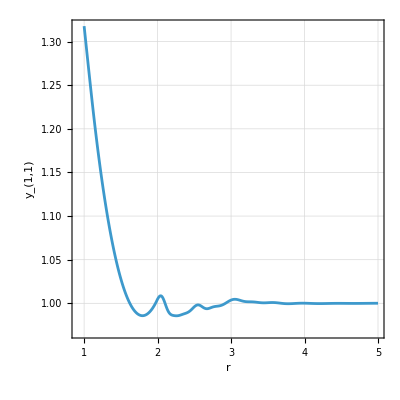

```mathematica
With[{i=1,j=1,rmax=5,Deltar=0.01},yExample[i,j]=Table[{r,y[r,i,j]},{r,sig[i,j],rmax,Deltar}];ListPlot[yExample[i,j],AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->All,Joined->True,FrameLabel->{"r",Subscript[y,i,j]}]]
```

Evaluation and plot of y_12(r) from r=σ_12 up to r=rmax  in steps of size Deltar

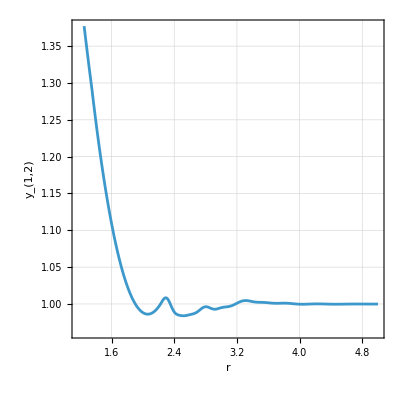

```mathematica
With[{i=1,j=2,rmax=5,Deltar=0.01},
yExample[i,j]=Table[{r,y[r,i,j]},{r,sig[i,j],rmax,Deltar}];
ListPlot[yExample[i,j],AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->All,Joined->True,FrameLabel->{"r",Subscript[y,i,j]}]]
```

Evaluation and plot of y_23(r) from r=σ_23 up to r=rmax  in steps of size Deltar

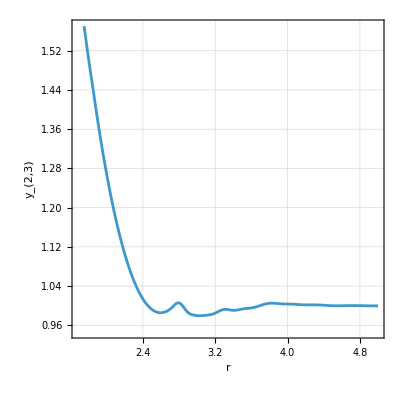

```mathematica
With[{i=2,j=3,rmax=5,Deltar=0.01},
yExample[i,j]=Table[{r,y[r,i,j]},{r,sig[i,j],rmax,Deltar}];
ListPlot[yExample[i,j],AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->All,Joined->True,FrameLabel->{"r",Subscript[y,i,j]}]]
```

Evaluation and plot of g_33(r) from r=σ_33 up to r=rmax in steps of size Deltar

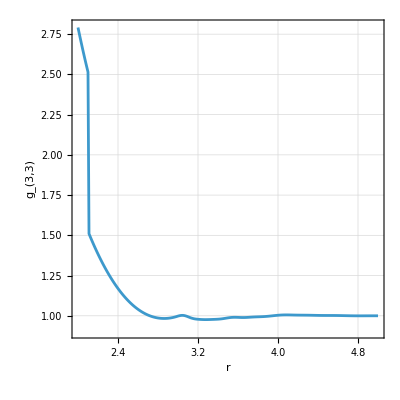

```mathematica
With[{i=3,j=3,rmax=5,Deltar=0.01},
gExample[i,j]=Table[{r,g[r,i,j]},{r,sig[i,j],rmax,Deltar}];
ListPlot[gExample[i,j],AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->{{sig[i,j],rmax},{0.9,2.8}},Joined->True,FrameLabel->{"r",Subscript[g,i,j]}]]
```

Evaluation and plot of  (h̃)_11(q)   from q=0 up to q=qmax in steps of size Deltaq

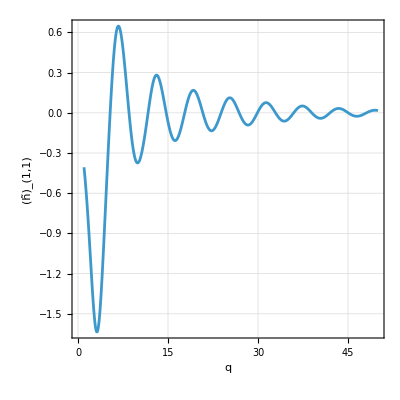

```mathematica
With[{i=1,j=1,qmax=50,Deltaq=0.1},
hqExample[i,j]=Table[{q,htilde[q,i,j]},{q,sig[i,j],qmax,Deltaq}];
ListPlot[hqExample[i,j],AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->All,Joined->True,FrameLabel->{"q",Subscript[h̃,i,j]}]]
```

Evaluation and plot of  (h̃)_13(q) from q=0 up to q=qmax in steps of size Deltaq

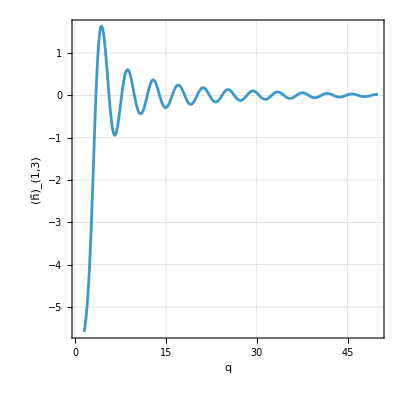

```mathematica
With[{i=1,j=3,qmax=50,Deltaq=0.1},
hqExample[i,j]=Table[{q,htilde[q,i,j]},{q,sig[i,j],qmax,Deltaq}];
ListPlot[hqExample[i,j],AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->All,Joined->True,FrameLabel->{"q",Subscript[h̃,i,j]}]]
```

## An instruction that leads to a more accurate, but slower, evaluation of g_ij(r) and y_ij(r)

If, for any reason, you need to verify a value  of  g_ij(r) (or y_ij(r), of course), or you suspect that numerical precision may be an issue in the numerical inversion of the Laplace transform used to obtain g_ij(r), simply use the following instruction:

```mathematica
(*Inverse Laplace transform of Subscript[G, ij]^0(s): Subscript[g, ij]^0(r) by means of the EulerILTplus algorithm *)
g0Asymm[r_,i_,j_]:=Which[r<sig[i,j],0,r<=λ[i,j],xiFINAL[r-sig[i,j],i,j]/r,r<=sig[i,j]+sigmaMin,xiFINAL[r-sig[i,j],i,j]/r+xibFINAL[r-λ[i,j],i,j]/r,r>sig[i,j]+sigmaMin,
EulerILTplus[myfun1, r-sig[i,j],{i,j}]/r+EulerILTplus[myfun2, r-λ[i,j],{i,j}]/r]
```

This instruction employs the routine EulerILTplus, which is somewhat more precise than EulerILT but also slower. The difference between the results obtained with the two routines is generally very small.  An example  of this  is given next.

#### An example

```mathematica
(*Inverse Laplace transform of Subscript[G, ij]^0(s): Subscript[g, ij]^0(r) by means of the EulerILTplus algorithm *) rmax=9;With[{i=1,j=1}, y11EulerILTplusTable=Table[{r,y[r,i,j]},{r,sig[i,j]+sigmaMin,rmax,0.1}]]
```

{{2.,1.00489},{2.1,1.0004},{2.2,0.986237},{2.3,0.986224},{2.4,0.989374},{2.5,0.995746},{2.6,0.996605},{2.7,0.994299},{2.8,0.996241},{2.9,0.999331},{3.,1.00348},{3.1,1.00395},{3.2,1.00195},{3.3,1.00148},{3.4,1.00109},{3.5,1.00073},{3.6,1.0003},{3.7,0.999977},{3.8,0.999887},{3.9,0.99991},{4.,0.999945},{4.1,0.999877},{4.2,0.999798},{4.3,0.999808},{4.4,0.999856},{4.5,0.999907},{4.6,0.999931},{4.7,0.999946},{4.8,0.999977},{4.9,1.00001},{5.,1.00003},{5.1,1.00004},{5.2,1.00003},{5.3,1.00003},{5.4,1.00002},{5.5,1.00001},{5.6,1.00001},{5.7,1.},{5.8,1.},{5.9,0.999999},{6.,0.999998},{6.1,0.999997},{6.2,0.999996},{6.3,0.999997},{6.4,0.999997},{6.5,0.999998},{6.6,0.999999},{6.7,0.999999},{6.8,1.},{6.9,1.},{7.,1.},{7.1,1.},{7.2,1.},{7.3,1.},{7.4,1.},{7.5,1.},{7.6,1.},{7.7,1.},{7.8,1.},{7.9,1.},{8.,1.},{8.1,1.},{8.2,1.},{8.3,1.},{8.4,1.},{8.5,1.},{8.6,1.},{8.7,1.},{8.8,1.},{8.9,1.},{9.,1.}}

```mathematica
(*Inverse Laplace transform of Subscript[G, ij]^0(s): Subscript[g, ij]^0(r) by means of the EulerILT algorithm *)
g0Asymm[r_,i_,j_]:=Which[r<sig[i,j],0,r<=λ[i,j],xiFINAL[r-sig[i,j],i,j]/r,r<=sig[i,j]+sigmaMin,xiFINAL[r-sig[i,j],i,j]/r+xibFINAL[r-λ[i,j],i,j]/r,r>sig[i,j]+sigmaMin,
EulerILT[myfun1, r-sig[i,j],{i,j}]/r+EulerILT[myfun2, r-λ[i,j],{i,j}]/r]
```

```mathematica
(*EulerILTplus*)rmax=9;With[{i=1,j=1}, y11EulerILTTable=Table[{r,y[r,i,j]},{r,sig[i,j]+sigmaMin,rmax,0.1}]]
```

{{2.,1.00489},{2.1,1.00034},{2.2,0.986373},{2.3,0.986227},{2.4,0.989154},{2.5,0.996043},{2.6,0.996454},{2.7,0.994213},{2.8,0.996584},{2.9,0.998877},{3.,1.00369},{3.1,1.004},{3.2,1.00193},{3.3,1.00162},{3.4,1.00072},{3.5,1.00071},{3.6,1.00079},{3.7,0.999881},{3.8,0.999556},{3.9,0.999984},{4.,1.00012},{4.1,0.999854},{4.2,0.999689},{4.3,0.999791},{4.4,0.999937},{4.5,0.999957},{4.6,0.9999},{4.7,0.999882},{4.8,0.999938},{4.9,1.00002},{5.,1.00007},{5.1,1.00008},{5.2,1.00006},{5.3,1.00003},{5.4,1.},{5.5,0.99998},{5.6,0.99997},{5.7,0.999975},{5.8,0.999992},{5.9,1.00001},{6.,1.00002},{6.1,1.00002},{6.2,1.00001},{6.3,1.},{6.4,0.999992},{6.5,0.999989},{6.6,0.99999},{6.7,0.999994},{6.8,0.999998},{6.9,1.},{7.,1.},{7.1,1.},{7.2,1.},{7.3,0.999999},{7.4,0.999999},{7.5,0.999999},{7.6,0.999999},{7.7,1.},{7.8,1.},{7.9,1.},{8.,1.},{8.1,1.},{8.2,1.},{8.3,1.},{8.4,1.},{8.5,1.},{8.6,1.},{8.7,1.},{8.8,1.},{8.9,1.},{9.,1.}}

Table with elements {r,ya(r)-yb(r)} where ya(r) denotes the values of  y11 obtained using  EulerILTplus  and  yb(r) are the values of y11 obtained with EulerILT.  The differences are very small

```mathematica
MapThread[{#1[[1]],#1[[2]]-#2[[2]]}&,{y11EulerILTplusTable,y11EulerILTTable}]
```

{{2.,0.},{2.1,0.0000556405},{2.2,-0.000135241},{2.3,-3.76322×10^-6},{2.4,0.000220154},{2.5,-0.000296798},{2.6,0.000151002},{2.7,0.0000863786},{2.8,-0.000343038},{2.9,0.000454184},{3.,-0.000214041},{3.1,-0.0000496589},{3.2,0.0000164504},{3.3,-0.000136614},{3.4,0.000373085},{3.5,0.0000215903},{3.6,-0.000486566},{3.7,0.0000957373},{3.8,0.000330422},{3.9,-0.0000732094},{4.,-0.00017716},{4.1,0.0000236619},{4.2,0.000108957},{4.3,0.000017281},{4.4,-0.000081446},{4.5,-0.0000500822},{4.6,0.0000312555},{4.7,0.0000645812},{4.8,0.0000387444},{4.9,-0.000012199},{5.,-0.0000429667},{5.1,-0.0000459821},{5.2,-0.0000293233},{5.3,-3.60495×10^-6},{5.4,0.0000190467},{5.5,0.000033977},{5.6,0.000037327},{5.7,0.0000274665},{5.8,7.86748×10^-6},{5.9,-0.0000131597},{6.,-0.0000262739},{6.1,-0.0000270957},{6.2,-0.0000177938},{6.3,-4.90207×10^-6},{6.4,5.08848×10^-6},{6.5,9.26612×10^-6},{6.6,8.3976×10^-6},{6.7,5.1274×10^-6},{6.8,1.90696×10^-6},{6.9,-5.95972×10^-8},{7.,-6.45486×10^-7},{7.1,-2.98343×10^-7},{7.2,4.2257×10^-7},{7.3,1.06442×10^-6},{7.4,1.3551×10^-6},{7.5,1.2418×10^-6},{7.6,8.26062×10^-7},{7.7,2.58723×10^-7},{7.8,-2.92819×10^-7},{7.9,-7.29045×10^-7},{8.,-1.00347×10^-6},{8.1,-1.10056×10^-6},{8.2,-1.04925×10^-6},{8.3,-8.96295×10^-7},{8.4,-6.98776×10^-7},{8.5,-5.04641×10^-7},{8.6,-3.38075×10^-7},{8.7,-2.17212×10^-7},{8.8,-1.35589×10^-7},{8.9,-8.67686×10^-8},{9.,-5.77121×10^-8}}